## H^⊗n |0⟩ state overlap

Notebook: Óscar Amaro, February 2024 @ GoLP-EPP

## Intro

Problem description: 
- Alice is informed that the number of qubits n describing a certain state |ψ⟩ is unknown
- Alice can produce a state |ϕ⟩ with a certain number of qubits m of her choice
- Alice can “call” for the overlap ⟨ϕ|ψ⟩ an infinite number of times, where the states are “tensored” with (1, 0)^T to adjust for the maximal number of qubits Max[n,m]
- Alice is given the information that the histogram of |ϕ⟩  is uniform
- Alice suspects that |ψ⟩  ~ H^(⊗n)|0⟩ 
- Alice could produce the state |ϕ⟩  ~ H^(⊗m)|0⟩ 
Can Alice easily determine m from the overlap? What is the most efficient strategy in number of “calls”?

## Possible solution

The further away n is from m, the lower the overlap
Since | ⟨ϕ|ψ⟩ | = | ⟨ψ|ϕ⟩ |, the problem should only depend on |n-m|, so it is symmetric around m
The state space increases as 2^m
One call is probably not enough because of the symmetry of the overlap
If the goal is also to minimize “computational resources” and if the overlap was “exact” (no noise), then one would try to minimize n such that Max[n,m] is also minimized
Calling n=1, if ⟨ϕ|ψ⟩=1 then m=n=1 and the problem is solved.
If ⟨ϕ|ψ⟩<1 then a theoretical scaling law of ⟨ϕ|ψ⟩ = f(n,m) should be invertible to retrieve m
Worst case scenario, 2 calls suffice
Solution ⟨ϕ|ψ⟩ = 2^(-|n-m|/2)

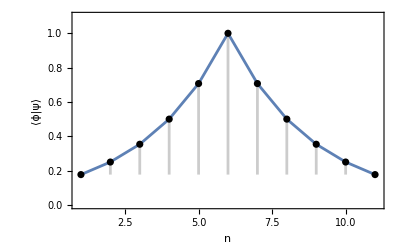

```mathematica
Clear[n,m,i,j,k,op,H,getOver,getOp]

(* Hadamard matrix *)
H=HadamardMatrix[2];
(* identity matrix *)
Id = IdentityMatrix[2];

(* the real number of qubits of |ψ⟩ *)
m=6;

(* compute results in range [1,nmax] *)
nmax=2m-1;

(* function to get operator *)
getOp[n_,m_]:=Module[{i,j,k,op},
op=1;

(* create H^n "guess" operator *)
For[i=1,i<=n,i++,
op=ArrayFlatten[TensorProduct[op,H]];
];

(* tensor the rest with Identity matrix *)
For[k=i,k<=m,k++,
op=ArrayFlatten[TensorProduct[op,Id]];
];

Return[op];
]

(* function to get the overlap ⟨ϕ|ψ⟩ *)
getOver[n_,m_]:=Module[{maxmn,Uϕ,Uψ,ϕ,ψ,zero},

(* maximum number of qubits *)
maxmn=Max[m,n];

(* operator to produce state |ϕ⟩ *)
Uϕ=getOp[If[n<=m,n,m],maxmn];

(* operator to produce state |ψ⟩ *)
Uψ=getOp[maxmn,maxmn];

(* state zero *)
zero=Table[KroneckerDelta[1,i],{i,1,2^maxmn}];

(* state |ψ⟩ *)
ψ=Uψ.zero;

(* state |ϕ⟩ *)
ϕ=Uϕ.zero;

Return[Conjugate[ϕ].ψ];
]

(* compute table *)
tab = ParallelTable[getOver[n,m],{n,1,nmax,1}];

(* plot *)
Show[{ListPlot[tab,Joined->{True,False},FrameLabel->{"n","⟨ϕ|ψ⟩"},Frame->True,PlotRange->{{0.9,nmax+0.1},{0,1.1}}],DiscretePlot[2^(-Abs[n-m]/2),{n,1,nmax},PlotStyle->Black]}]
```